## Definition

```mathematica
ConjugateTranspose[({{ⅈ, 0, 0, 0}, {0, 0, -ⅈ, 0}, {0, 0, 0, -ⅈ}, {0, ⅈ, 0, 0}})].Simplify[{{a kz,0,-(a+3b)/4(kx+I ky),(√3)/4(a-b)(kx-I ky)},{0,b kz,(√3)/4(a-b)(kx-I ky),-(3a+b)/4(kx+I ky)},{-(a+3b)/4(kx-I ky),(√3)/4(a-b)(kx+I ky),-a kz,0},{(√3)/4(a-b)(kx+I ky),-(3a+b)/4(kx-I ky),0,-b kz}}].({{ⅈ, 0, 0, 0}, {0, 0, -ⅈ, 0}, {0, 0, 0, -ⅈ}, {0, ⅈ, 0, 0}})//MatrixForm
```

(a kz | 1/4 √3 (a-b) (kx-ⅈ ky) | 0 | 1/4 (a+3 b) (kx+ⅈ ky)
1/4 √3 (a-b) (kx+ⅈ ky) | -b kz | 1/4 (3 a+b) (kx-ⅈ ky) | 0
0 | 1/4 (3 a+b) (kx+ⅈ ky) | b kz | 1/4 √3 (a-b) (kx-ⅈ ky)
1/4 (a+3 b) (kx-ⅈ ky) | 0 | 1/4 √3 (a-b) (kx+ⅈ ky) | -a kz)

```mathematica
H[a_,b_,kx_,ky_,kz_]:=({{a kz, 1/4 √3 (a-b) (kx-ⅈ ky), 0, 1/4 (a+3 b) (kx+ⅈ ky)}, {1/4 √3 (a-b) (kx+ⅈ ky), -b kz, 1/4 (3 a+b) (kx-ⅈ ky), 0}, {0, 1/4 (3 a+b) (kx+ⅈ ky), b kz, 1/4 √3 (a-b) (kx-ⅈ ky)}, {1/4 (a+3 b) (kx-ⅈ ky), 0, 1/4 √3 (a-b) (kx+ⅈ ky), -a kz}})
```

```mathematica
PropagatorS[ω_,kx_,ky_,kz_,a_,b_]:=Inverse[-ⅈ ω IdentityMatrix[4]+H[a,b,kx,ky,kz]]
PropagatorS[ω,kx,ky,kz,1,0]//MatrixForm
```

(((9 kx^2 kz)/16+(9 ky^2 kz)/16+3/4 ⅈ kx^2 ω+3/4 ⅈ ky^2 ω+kz ω^2+ⅈ ω^3)/((9 kx^2 ky^2)/16+(9 kx^2 kz^2)/16+(9 ky^2 kz^2)/16+kx^2 ω^2+ky^2 ω^2+kz^2 ω^2+ω^4) | (-3/16 ⅈ √3 kx^2 ky+3/16 √3 kx ky^2-1/4 ⅈ √3 kx kz ω-1/4 √3 ky kz ω+1/4 √3 kx ω^2-1/4 ⅈ √3 ky ω^2)/((9 kx^2 ky^2)/16+(9 kx^2 kz^2)/16+(9 ky^2 kz^2)/16+kx^2 ω^2+ky^2 ω^2+kz^2 ω^2+ω^4) | (-3/16 √3 kx^2 kz+3/8 ⅈ √3 kx ky kz+3/16 √3 ky^2 kz-1/4 ⅈ √3 kx^2 ω-1/4 √3 kx ky ω+1/4 ⅈ √3 ky^2 ω)/((9 kx^2 ky^2)/16+(9 kx^2 kz^2)/16+(9 ky^2 kz^2)/16+kx^2 ω^2+ky^2 ω^2+kz^2 ω^2+ω^4) | (9/16 ⅈ kx^2 ky+(9 kx ky^2)/16+(kx ω^2)/4+1/4 ⅈ ky ω^2)/((9 kx^2 ky^2)/16+(9 kx^2 kz^2)/16+(9 ky^2 kz^2)/16+kx^2 ω^2+ky^2 ω^2+kz^2 ω^2+ω^4)
(3/16 ⅈ √3 kx^2 ky+3/16 √3 kx ky^2-1/4 ⅈ √3 kx kz ω+1/4 √3 ky kz ω+1/4 √3 kx ω^2+1/4 ⅈ √3 ky ω^2)/((9 kx^2 ky^2)/16+(9 kx^2 kz^2)/16+(9 ky^2 kz^2)/16+kx^2 ω^2+ky^2 ω^2+kz^2 ω^2+ω^4) | (-(3 kx^2 kz)/16-(3 ky^2 kz)/16+1/4 ⅈ kx^2 ω+1/4 ⅈ ky^2 ω+ⅈ kz^2 ω+ⅈ ω^3)/((9 kx^2 ky^2)/16+(9 kx^2 kz^2)/16+(9 ky^2 kz^2)/16+kx^2 ω^2+ky^2 ω^2+kz^2 ω^2+ω^4) | (-3/16 ⅈ kx^2 ky+(3 kx ky^2)/16+(3 kx kz^2)/4-3/4 ⅈ ky kz^2+(3 kx ω^2)/4-3/4 ⅈ ky ω^2)/((9 kx^2 ky^2)/16+(9 kx^2 kz^2)/16+(9 ky^2 kz^2)/16+kx^2 ω^2+ky^2 ω^2+kz^2 ω^2+ω^4) | (3/16 √3 (kx-ⅈ ky)^2 (kz-ⅈ ω)-1/16 ⅈ √3 (kx+ⅈ ky)^2 ω)/((9 kx^2 ky^2)/16+(9 kx^2 kz^2)/16+(9 ky^2 kz^2)/16+kx^2 ω^2+ky^2 ω^2+kz^2 ω^2+ω^4)
(-3/16 √3 kx^2 kz-3/8 ⅈ √3 kx ky kz+3/16 √3 ky^2 kz-1/4 ⅈ √3 kx^2 ω+1/4 √3 kx ky ω+1/4 ⅈ √3 ky^2 ω)/((9 kx^2 ky^2)/16+(9 kx^2 kz^2)/16+(9 ky^2 kz^2)/16+kx^2 ω^2+ky^2 ω^2+kz^2 ω^2+ω^4) | (3/16 ⅈ kx^2 ky+(3 kx ky^2)/16+(3 kx kz^2)/4+3/4 ⅈ ky kz^2+(3 kx ω^2)/4+3/4 ⅈ ky ω^2)/((9 kx^2 ky^2)/16+(9 kx^2 kz^2)/16+(9 ky^2 kz^2)/16+kx^2 ω^2+ky^2 ω^2+kz^2 ω^2+ω^4) | ((3 kx^2 kz)/16+(3 ky^2 kz)/16+1/4 ⅈ kx^2 ω+1/4 ⅈ ky^2 ω+ⅈ kz^2 ω+ⅈ ω^3)/((9 kx^2 ky^2)/16+(9 kx^2 kz^2)/16+(9 ky^2 kz^2)/16+kx^2 ω^2+ky^2 ω^2+kz^2 ω^2+ω^4) | (-3/16 ⅈ √3 kx^2 ky+3/16 √3 kx ky^2+1/4 ⅈ √3 kx kz ω+1/4 √3 ky kz ω+1/4 √3 kx ω^2-1/4 ⅈ √3 ky ω^2)/((9 kx^2 ky^2)/16+(9 kx^2 kz^2)/16+(9 ky^2 kz^2)/16+kx^2 ω^2+ky^2 ω^2+kz^2 ω^2+ω^4)
(-9/16 ⅈ kx^2 ky+(9 kx ky^2)/16+(kx ω^2)/4-1/4 ⅈ ky ω^2)/((9 kx^2 ky^2)/16+(9 kx^2 kz^2)/16+(9 ky^2 kz^2)/16+kx^2 ω^2+ky^2 ω^2+kz^2 ω^2+ω^4) | (3/16 √3 kx^2 kz+3/8 ⅈ √3 kx ky kz-3/16 √3 ky^2 kz-1/4 ⅈ √3 kx^2 ω+1/4 √3 kx ky ω+1/4 ⅈ √3 ky^2 ω)/((9 kx^2 ky^2)/16+(9 kx^2 kz^2)/16+(9 ky^2 kz^2)/16+kx^2 ω^2+ky^2 ω^2+kz^2 ω^2+ω^4) | (3/16 ⅈ √3 kx^2 ky+3/16 √3 kx ky^2+1/4 ⅈ √3 kx kz ω-1/4 √3 ky kz ω+1/4 √3 kx ω^2+1/4 ⅈ √3 ky ω^2)/((9 kx^2 ky^2)/16+(9 kx^2 kz^2)/16+(9 ky^2 kz^2)/16+kx^2 ω^2+ky^2 ω^2+kz^2 ω^2+ω^4) | (-(9 kx^2 kz)/16-(9 ky^2 kz)/16+3/4 ⅈ kx^2 ω+3/4 ⅈ ky^2 ω-kz ω^2+ⅈ ω^3)/((9 kx^2 ky^2)/16+(9 kx^2 kz^2)/16+(9 ky^2 kz^2)/16+kx^2 ω^2+ky^2 ω^2+kz^2 ω^2+ω^4))

## Polarization

```mathematica
BetaG[a_,b_,δϕ_]:=NIntegrate[Re[Sin[θ]/(2π)^4 Simplify[D[Tr[PropagatorS[ω,Sin[θ]Cos[ϕ]+q,Sin[θ]Sin[ϕ],Cos[θ],a,b].PropagatorS[ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ],a,b]],{q,2}]/.q->0]],{ω,-Infinity,Infinity},{θ,δϕ,π/2-δϕ},{ϕ,0,2π}]+NIntegrate[Re[Sin[θ]/(2π)^4 Simplify[D[Tr[PropagatorS[ω,Sin[θ]Cos[ϕ]+q,Sin[θ]Sin[ϕ],Cos[θ],a,b].PropagatorS[ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ],a,b]],{q,2}]/.q->0]],{ω,-Infinity,Infinity},{θ,π/2+δϕ,π-δϕ},{ϕ,0,2π}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in ϕ near {ω,θ,ϕ} = {8.93573×10^-9,1.5707962940697864580159218248876383441231530113668668491300195456,4.71239}. NIntegrate obtained -160189. and 95085.5 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.629969 and 6.10902×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in ϕ near {ω,θ,ϕ} = {8.93573×10^-9,1.5707963595200066579820416436565468174674231605081331508699804544,4.71239}. NIntegrate obtained -160189. and 95085.5 for the integral and error estimates.

{-320378.,0.}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.629969 and 6.10902×10^-6 for the integral and error estimates.

{-1.25994,0.025}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.12823 and 0.0000366026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.525753 and 4.69854×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.12823 and 0.0000366026 for the integral and error estimates.

{-6.25646,0.005}

{-1.05151,0.03}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.56704 and 0.0000216966 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{-3.13407,0.01}

{-0.902542,0.035}

{-2.09308,0.015}

{-0.790748,0.04}

{-1.57244,0.02}

{-0.703731,0.045}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.317029 and 2.37393×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.212228 and 1.5304×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.317029 and 2.37393×10^-6 for the integral and error estimates.

{-0.634058,0.05}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.212228 and 1.5304×10^-6 for the integral and error estimates.

{-0.424455,0.075}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.2885 and 2.11316×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.199072 and 1.10093×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{-0.577001,0.055}

{-0.398144,0.08}

{-0.529404,0.06}

{-0.374894,0.085}

{-0.489084,0.065}

{-0.354194,0.09}

{-0.454482,0.07}

{-0.335642,0.095}

{{0.,-320378.},{0.005,-6.25646},{0.01,-3.13407},{0.015,-2.09308},{0.02,-1.57244},{0.025,-1.25994},{0.03,-1.05151},{0.035,-0.902542},{0.04,-0.790748},{0.045,-0.703731},{0.05,-0.634058},{0.055,-0.577001},{0.06,-0.529404},{0.065,-0.489084},{0.07,-0.454482},{0.075,-0.424455},{0.08,-0.398144},{0.085,-0.374894},{0.09,-0.354194},{0.095,-0.335642}}

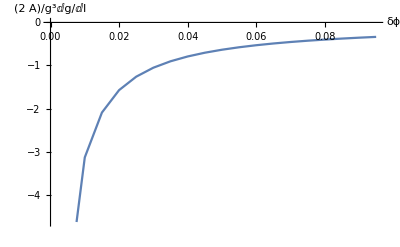

```mathematica
data1=ParallelTable[(y=BetaG[1,0,0.005(i-1)];Print[{y,0.005(i-1)}];{0.005(i-1),y}),{i,1,20}]
ListLinePlot[data1,AxesLabel->{"δϕ","(2  A)/g^3ⅆg/ⅆl"}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in ϕ near {ω,θ,ϕ} = {8.93573×10^-9,1.5707962940697864580159218248876383441231530113668668491300195456,4.71239}. NIntegrate obtained -160189. and 95085.5 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.629969 and 6.10902×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in ϕ near {ω,θ,ϕ} = {8.93573×10^-9,1.5707963595200066579820416436565468174674231605081331508699804544,4.71239}. NIntegrate obtained -160189. and 95085.5 for the integral and error estimates.

{-320378.,0.}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.629969 and 6.10902×10^-6 for the integral and error estimates.

{-1.25994,0.025}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.12823 and 0.0000366026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.525753 and 4.69854×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.12823 and 0.0000366026 for the integral and error estimates.

{-6.25646,0.005}

{-1.05151,0.03}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.56704 and 0.0000216966 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{-3.13407,0.01}

{-0.902542,0.035}

{-2.09308,0.015}

{-0.790748,0.04}

{-1.57244,0.02}

{-0.703731,0.045}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.317029 and 2.37393×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.212228 and 1.5304×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.317029 and 2.37393×10^-6 for the integral and error estimates.

{-0.634058,0.05}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.212228 and 1.5304×10^-6 for the integral and error estimates.

{-0.424455,0.075}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.2885 and 2.11316×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.199072 and 1.10093×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{-0.577001,0.055}

{-0.398144,0.08}

{-0.529404,0.06}

{-0.374894,0.085}

{-0.489084,0.065}

{-0.354194,0.09}

{-0.454482,0.07}

{-0.335642,0.095}

{{0.,-320378.},{0.005,-6.25646},{0.01,-3.13407},{0.015,-2.09308},{0.02,-1.57244},{0.025,-1.25994},{0.03,-1.05151},{0.035,-0.902542},{0.04,-0.790748},{0.045,-0.703731},{0.05,-0.634058},{0.055,-0.577001},{0.06,-0.529404},{0.065,-0.489084},{0.07,-0.454482},{0.075,-0.424455},{0.08,-0.398144},{0.085,-0.374894},{0.09,-0.354194},{0.095,-0.335642}}

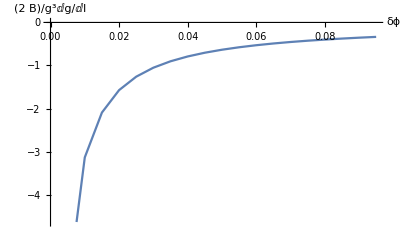

```mathematica
data2=ParallelTable[(y=BetaG[0,1,0.005(i-1)];Print[{y,0.005(i-1)}];{0.005(i-1),y}),{i,1,20}]
ListLinePlot[data1,AxesLabel->{"δϕ","(2  B)/g^3ⅆg/ⅆl"}]
```

```mathematica
SphericalPlot3D[{1,-1},{θ,0.1,π/2-0.1},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
NIntegrate[Re[Sin[θ]/(2π)^4 Simplify[D[Tr[PropagatorS[ω,Sin[θ]Cos[ϕ]+q,Sin[θ]Sin[ϕ],Cos[θ],1,0.01].PropagatorS[ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ],1,0.01]],{q,2}]/.q->0]],{ω,-Infinity,Infinity},{θ,0,π},{ϕ,0,2π}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.35654 and 0.000293834 for the integral and error estimates.

-3.35654

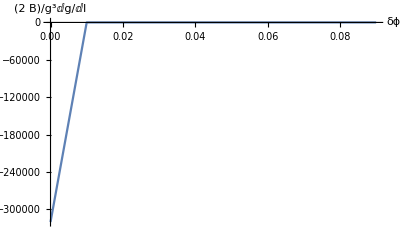

```mathematica
ListLinePlot[data2,AxesLabel->{"δϕ","(2  B)/g^3ⅆg/ⅆl"},PlotRange->All]
```